```mathematica
Λ[t_,b_,d_]:=Max[{0,Min[{t-b,d-t}]}]
λ[t_,k_,bd_]:=Module[{l={},i=1},
For[i=1,i≤Length[bd],i++,AppendTo[l,Λ[t,bd[[i]][[1]],bd[[i]][[2]]]]];
Return[Sort[l,(#1>#2)&][[k]]]]
```

```mathematica
bd={{0.5978,1.0064},{0.8857,1.2557},{0.7500,0.9235},{0.9245,1.0811},{0.3833,0.4687},{0.3684,0.4491},{0.7118,0.7398},{0.7352,0.7495}}
```

{{0.5978,1.0064},{0.8857,1.2557},{0.75,0.9235},{0.9245,1.0811},{0.3833,0.4687},{0.3684,0.4491},{0.7118,0.7398},{0.7352,0.7495}}

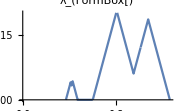
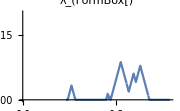
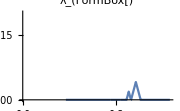
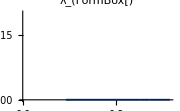
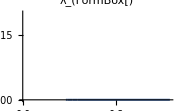
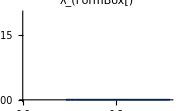
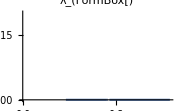
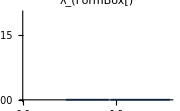

```mathematica
Table[Plot[λ[t,i,bd],{t,Min[bd],Max[bd]}, PlotRange->{{0,Max[bd]},{0,0.2}}, ImageSize-> Small, PlotLabel->Style[StringForm["λ_(``)", i], FontSize->14, FontWeight->Bold]],{i,1,Length[bd]}]
```

```mathematica
functions = Table[λ[k,i,bd], {i,1,Length[bd]}];
legends = Table[StringForm["λ_(``)", i],{i,1,Length[bd]}];
```

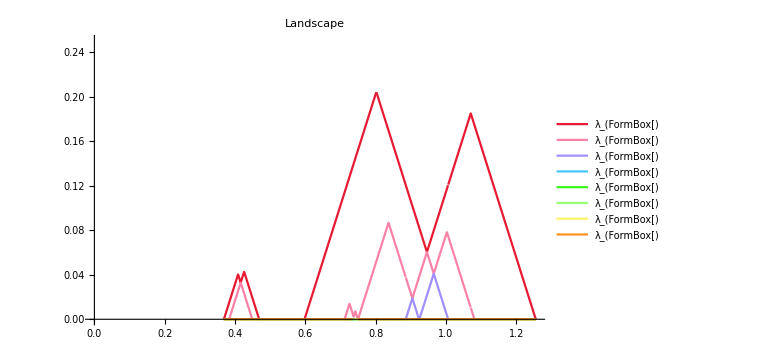

```mathematica
r = Plot[{λ[k,1,bd], λ[k,2,bd], λ[k,3,bd], λ[k,4,bd], λ[k,5,bd], λ[k,6,bd], λ[k,7,bd],λ[k,8,bd]},{k,Min[bd],Max[bd]}, PlotRange->{{0,Max[bd]},{0,0.25}}, ImageSize->Large, PlotLabel->"Landscape", PlotLegends->legends, PlotStyle->Table[ColorData["BrightBands"][k], {k,0,1,1/Length[bd]}]]
```